```mathematica
ClearAll["Global'*"]
LHS = FullSimplify[Assuming[{c>R>0},∫_R^c n A ((Eo c^2)/(No r^2)-Eo/No)ⅆr]];
RHS = Log[Q];
Sol1 = FullSimplify[Flatten[Solve[LHS==RHS,c]]]
c = Normal[c/.Sol1[[2]]]
```

{c→R-(√No √R √Log[Q])/(√A √Eo √n),c→R+(√No √R √Log[Q])/(√A √Eo √n)}

R+(√No √R √Log[Q])/(√A √Eo √n)

```mathematica
Vc[R_] = δ R Eo(c/R)^2;
Sol2 = Flatten[Solve[D[Vc[R], R]==0,R]]
```

{R→(No Log[Q])/(A Eo n)}

```mathematica
Vmin = Vc[R]/.Sol2;
Rmin = R/.Sol2;
Print["Vc[R] = ",Vc[R], " (V)"];
Print["Rmin = ",Rmin, " (m)"];
Print["Vmin = ",Vmin, " (V)"];
```

Vc[R] = (Eo δ (R+(√No √R √Log[Q])/(√A √Eo √n))^2)/R (V)

Rmin = (No Log[Q])/(A Eo n) (m)

Vmin = (A Eo^2 n δ ((No Log[Q])/(A Eo n)+(√No √Log[Q] √((No Log[Q])/(A Eo n)))/(√A √Eo √n))^2)/(No Log[Q]) (V)

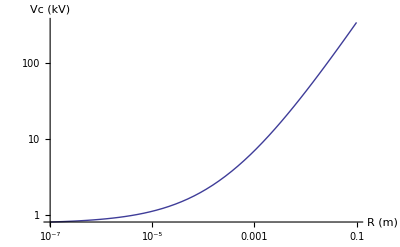

```mathematica
A = 0.012;
Q = 10^4;
p= 101325;
δ = 1;
No = 2.688 10^19 10^6;
n = No;
Eo = 31 10^5;
R2 = 1000;
LogLogPlot[Vc[R]/1000, {R,10^-7,10^-1}, AxesLabel-> {"R (m)", "Vc (kV)"}]
```